```mathematica
ClearAll["Global`*"]
```

```mathematica
<<ExaminePareto`
```

2.1. When we are doing science we might be in a situation where we have collected data and found that it fits a Pareto Distribution. One way we can use past data is to predict to future values. This can be dangerous if our predictions are wrong. Lets say the higher the value of X the greater the cost/the higher the damage. In cases like this we might want to know how likely is it that we will see a value that is greater than any value we have see already. To create the histogram below we run 100 experiments. In each experiment we take a sample of 40 values for a Pareto Distribution with shape (1.5). We then take a further 1000 numbers and see what percentage of them is greater than the max we saw from the first 40. We create a Histogram of the results. We can say that for about 38 of the experiments the percentage of values greater than the max was less than 1%. We can also see that for some experiments there were more than 8% of the values greater than the max. We will refer to this metric as ‘PercentsBiggerThanMax’.

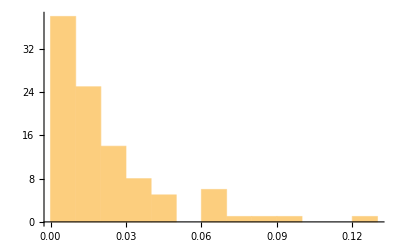

```mathematica
Histogram[PercentsBiggerThanMax[1.5,100,1000,40]]
```

```mathematica
Table[i+i+i+2, {i,10,100,10}]
```

{32,62,92,122,152,182,212,242,272,302}

```mathematica
(1/Mean[PercentsBiggerThanMax[1.5,100,1000,10]])
```

11.2651

```mathematica
((1/Mean[PercentsBiggerThanMax[1.5,100,1000,20]])/20)
```

0.933881

```mathematica
Table[ (1/Mean[PercentsBiggerThanMax[1.5,100,1000,i]])/i, {i,10,200,10}]
```

{0.0112247,0.0185792,0.029982,0.0472564,0.0513889,0.063268,0.0820198,0.077024,0.092844,0.105158,0.0889582,0.121238,0.145627,0.125188,0.139525,0.163235,0.188136,0.205556,0.160096,0.233958}

2.2. This next 3D Histogram shows us what happens to PercentsBiggerThanMax as we vary the number of initial samples (in the Z axis i.e. going away from you the viewer). Each 'frame' parallel to the screen is equivalent to one of the above Histograms from (2.1). As the number of initial samples goes up the number of times we see values far in excess of initial max goes down. PercentsBiggerThanMax bunches up close to 0.

```mathematica
ForRangeSamplesHistogram3D[PercentsBiggerThanMax,
200,
10,100,10,
1.0, 
1000,
 {0.005},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

2.3. The Histogram below show us what happens as we vary the value of the shape parameter in the same way that we varied samples in (2.2) above. Here we seem to see that it has no effect on how often and to what extent we see a different distribution of results.

```mathematica
ForRangeShapeHistogram3D[PercentsBiggerThanMax,
200,
0.1,2,0.1,
1000,
40,
 {0.005},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

2.4. Here we run the same test as (2.3) above but for a larger initial sample size (100 instead of 40). Again we seem to see that varying shape has no affect.

```mathematica
ForRangeShapeHistogram3D[PercentsBiggerThanMax,
200,
0.1,2,0.1,
1000,
100,
 {0.005},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-